# Physics 234 Final Project Draft 2

Eric Shao, Ziyang Gao
5/2018

## Section 0: Progress report

Process and concerns: We’ve finished building up all the necessary functions for a complete simulation of a simplified two-lane road diet problem. And we’ve also built a high level function that integrate the functions, including updatev[list_,SL_], updatep[list_], simplewantemerge[p_,listofsign_,list_] and merge[list1_,list2_] to a self-run traffic simulator. However, we have some bugs in one or some of the functions that are causing some error messages below that we are having trouble to understand. By this Tuesday, we will finish looking into the details of each function and try to clear all the potential typos that are leading to the bug. And we will also complete the animation part of the simplified simulation.

```mathematica
(*Findpos[pos_,list_]:=Module[
{l=Length[list],returnvalue=-1},
For[i≤ l,i++,
If[list[[i]][[1]]==pos,returnvalue=i],
If[list[[i]][[1]]<pos,break]];
returnvalue
];*)
```

```mathematica
updatev1[list_,SL_]:=Module[
{L=Length[list],d,templist=list},
For[i=2,i≤ L,i++,
d=list[[i,1]]-list[[i-1,1]];
If[d<SL,
templist=ReplacePart[templist,{i,2}->SL+SL*0.2],
templist=ReplacePart[templist,{i,2}->Floor[list[[i,2]]/2]];
];
If[templist[[i,2]]<0,templist[[i,2]]=0];
];
templist
]
```

```mathematica
updatev2[list_,SL_, lanelength_]:=Module[
{L=Length[list],d,templist=list},
For[i=2,i≤ L,i++,
If[templist[[i,1]]<lanelength-2*SL,
{
d=list[[i,1]]-list[[i-1,1]];
If[d<SL,
templist=ReplacePart[templist,{i,2}->SL+SL*0.2],
templist=ReplacePart[templist,{i,2}->Floor[list[[i,2]]/2]];
];
},
{
templist=ReplacePart[templist,{i,2} -> Floor[list[[i,2]]/2]];
}];
If[templist[[i,2]]<0,templist[[i,2]]=0];
];
templist
]
```

```mathematica
updatep1[list_]:=Module[
{L=Length[list],templist=list},
templist=ReplacePart[templist,{1,1}-> templist[[1,1]]+templist[[1,2]] ];
If[L≥2,
For[i=2,i≤ L,i++,
If[templist[[i,1]]+templist[[i,2]]<templist[[i-1,1]]-5,
templist=ReplacePart[templist,{i,1}-> templist[[i,1]]+templist[[i,2]] ]  ]; 
];
];
templist
]
```

```mathematica
updatep2[list_,lanelength_]:=Module[
{L=Length[list],templist=list},
If[L≥2,
templist=ReplacePart[templist,{1,1}-> templist[[1,1]]+templist[[1,2]] ];
For[i=2,i≤ L,i++,
If[templist[[i,1]]+templist[[i,2]]<templist[[i-1,1]]-5,
templist=ReplacePart[templist,{i,1}-> templist[[i,1]]+templist[[i,2]] ]  ]; 
];
];
If[L≥ 1,
For[k=1,k≤Length[templist],k++,
If[templist[[k,1]]≥ lanelength-templist[[k,2]],templist[[k,2]]=0];
];
For[k=1,k≤Length[templist],k++,
If[templist[[k,1]]>lanelength,templist[[k,1]]=lanelength];
];
];
If[L==1,
templist[[1,1]]=templist[[1,2]]+templist[[1,1]]
];
templist
]
```

```mathematica
wantomerge[p_,listofsign_,list_,lanelength_,SL_]:=Module[
{L=Length[list],a,b,templist=list},
For[i=1,i≤ L,i++,
a=list[[i,1]];
b=a+list[[i,2]];
For [k=1,k≤Length[listofsign],k++,
If[a<listofsign[[k]]&&b>listofsign[[k]]&&p>RandomReal[],templist=ReplacePart[templist,{i,3}-> 1]  ]  ];
If[list[[i,1]]>lanelength-2*SL,templist=ReplacePart[templist,{i,3}-> 1] ];
];
templist
]
```

```mathematica
merge[list1_,list2_,SL_]:=Module[
{addin,new1=list1,index={},a=0,list3},
For[i=1,i≤Length[list2],i++,
addin=list2[[i]][[1;;2]];
a=0;
For[k=list2[[i,1]]-SL,k≤list2[[i,1]]+SL,k++,
If[MemberQ[list1[[All,1]],k],a=1];
];
If[a==0&&list2[[i,3]]==1,
AppendTo[new1,addin]; AppendTo[index,{i}]
];
];
new1=Sort[new1,#1[[1]]>#2[[1]]&];
list3=Delete[list2,index];
{new1,list3}
]
```

```mathematica
realrundemo[SL_,nsign_,TI_]:=Module[
{Lane1={{0,38}},Lane2={{0,38,0}},t=1, process={},jointLanes},
For[t=0,t≤200,t++,
If[Mod[t,TI]==0,
i=RandomInteger[];
If[i==0,
AppendTo[Lane2,{0,RandomInteger[{SL-3,SL+3}],0}],
AppendTo[Lane1,{0,RandomInteger[{SL-3,SL+3}]}]
]];
If[Length[Lane1]>0&&Length[Lane2]>0,
Lane1=updatev1[Lane1,SL];
Lane2=updatev2[Lane2,SL,1000];
Lane1=updatep1[Lane1];
Lane2=updatep2[Lane2,1000];
Lane2=wantomerge[0.4,nsign,Lane2,1000,SL];
jointLanes=merge[Lane1,Lane2,SL];
Lane1=jointLanes[[1]];
Lane2=jointLanes[[2]];
];
AppendTo[process,{Lane1,Lane2}];
];
For[j=1,j≤10000,j++,
Lane1=updatev1[Lane1,SL];
Lane2=updatev2[Lane2,SL,1000];
Lane1=updatep1[Lane1];
Lane2=updatep2[Lane2,1000];
Lane2=wantomerge[0.4,nsign,Lane2,1000,SL];
jointLanes=merge[Lane1,Lane2,SL];
Lane1=jointLanes[[1]];
Lane2=jointLanes[[2]];
AppendTo[process,{Lane1,Lane2}];
If[Length[Lane2]==0,j=10001];
];
process
]
```

```mathematica
realrundemo[30,{500},5]
```

```mathematica
k={Length[realrundemo[10,{},1]],
Length[realrundemo[10,{500},1]],
Length[realrundemo[10,{333,666},1]],
Length[realrundemo[10,{250,500,750},1]],
Length[realrundemo[10,{200,400,600,800},1]],
Length[realrundemo[10,{166,333,499,665,831},1]],
Length[realrundemo[10,{142,284,426,568,710,852},1]],
Length[realrundemo[10,{125,250,375,500,625,750,875},1]],
Length[realrundemo[10,{111,222,333,444,555,666,777,888},1]],Length[realrundemo[10,{100,200,300,400,500,600,700,800,900},1]],
Length[realrundemo[10,{90,180,270,360,450,540,630,720,810,900},1]],Length[realrundemo[10,{83,166,249,332,415,498,581,664,747,830,913},1]],Length[realrundemo[10,{76,152,228,304,380,456,532,608,684,760,836,912},1]],Length[realrundemo[10,{71,142,213,289,365,436,507,578,649,720,791,826,933},1]],Length[realrundemo[10,{66,132,198,264,330,396,462,528,594,660,726,792,858,924},1]],Length[realrundemo[10,{63,126,189,252,315,378,441,504,567,630,693,756,819,882,945},1]],Length[realrundemo[10,{58,116,174,232,290,348,406,464,522,580,638,696,754,812,870,928},1]],Length[realrundemo[10,{55,110,165,220,275,330,385,440,495,550,605,660,715,770,825,880,935},1]],Length[realrundemo[10,{52,104,156,208,260,312,364,416,468,520,572,624,676,728,780,832,884，936},1]],Length[realrundemo[10,{50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850，900，950},1]]
};
k
```

{281,281,270,282,282,277,267,246,278,278,275,239,265,213,247,229,233,230,227,217}

```mathematica
data={{282,268,248,260,266,233,244,238,238,228,272,237,225,211,254,242,222,238,228,284},{282,282,270,282,258,268,274,231,241,278,274,207,280,213,230,236,202,223,222,217},{278,274,272,280,272,239,252,272,227,256,237,227,249,228,220,224,212,209,233,229},{282,282,264,276,278,239,280,238,266,254,256,248,223,234,230,216,217,214,213,254},{282,276,274,266,276,262,229,223,226,206,252,232,284,205,241,211,213,248,217,202},{276,278,276,262,282,276,233,216,276,252,282,248,225,216,230,224,214,219,272,256},{272,282,280,272,268,259,241,229,247,272,250,216,280,224,222,209,230,250,233,203},{282,270,274,274,258,267,219,248,227,230,235,230,222,228,252,236,286,216,217,284},{280,278,254,256,258,246,259,276,264,209,263,245,229,216,260,209,211,220,241,242},{282,274,276,268,280,274,260,235,235,246,278,213,225,204,208,223,248,207,276,217},{282,270,272,278,274,247,241,244,264,221,252,223,238,280,259,204,234,206,208,208},{268,282,255,264,274,248,250,264,272,229,248,234,227,217,262,215,207,206,217,208},{276,273,282,277,277,253,262,269,242,270,266,226,263,228,240,266,284,262,217,230},{268,280,282,282,266,276,274,252,221,268,250,225,220,230,211,245,207,207,232,234},{282,282,282,268,274,235,251,282,272,266,276,226,270,224,263,313,217,221,217,252},{282,282,266,270,278,231,253,220,230,262,258,225,208,240,253,213,223,220,208,229},{282,278,280,262,276,251,225,250,260,274,237,210,243,211,268,219,252,216,237,210},{282,280,268,262,276,268,243,247,270,266,256,224,219,237,256,259,234,219,206,231},{282,280,270,270,278,250,211,223,246,241,242,253,232,207,230,223,232,270,214,277},{274,282,274,276,250,270,258,256,227,241,235,214,223,250,269,241,234,209,212,252}};
```

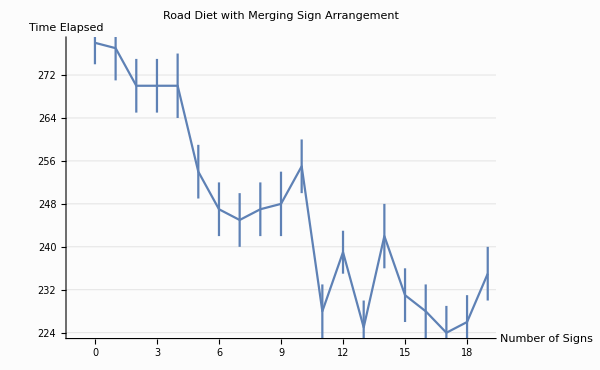

```mathematica
meandata=Floor[Mean[data]];
standardError[ts_]:=StandardDeviation[ts]/Sqrt[20];
stderrordata=Floor[standardError/@data];
Needs["ErrorBarPlots`"];
plotData=Partition[Riffle[meandata,stderrordata],2];
tickSpecs={ {{1,"0"},{2,"1"},{3,"2"},{4,"3"},{5,"4"},{6,"5"},{7,"6"},{8,"7"},{9,"8"},{10,"9"},{11,"10"},{12,"11"},{13,"12"},{14,"13"},{15,"14"},{16,"15"},{17,"16"},{18,"17"},{19,"18"},{20,"19"}} ,Automatic};

ErrorListPlot[plotData, Frame->{Left,Bottom}, Ticks->tickSpecs,AxesLabel->{Style["Number of Signs",12,FontFamily->"Arial"],Style["Time Elapsed",12,FontFamily->"Arial"]},Joined->True,GridLines->Automatic,PlotLabel->"Road Diet with Merging Sign Arrangement",ImageSize->600,Background->GrayLevel[0.99]]
```

```mathematica
datafor99=Range[10,990,10];
datafor90=Range[11,999,11];
datafor82 =Range[12,995,12];
datafor70 =Range[14,993,14];
datafor61=Range[16,976,16];
datafor49=Range[20,981,20];
datafor39=Range[25,999,25];
datafor29=Range[33,989,33];
datafor19=Range[50,999,50];
datafor9=Range[100,990,100];
```

```mathematica
sample={Length[realrundemo[10,datafor9,1]],Length[realrundemo[10,datafor19,1]],Length[realrundemo[10,datafor29,1]],Length[realrundemo[10,datafor39,1]],Length[realrundemo[10,datafor49,1]],Length[realrundemo[10,datafor61,1]],Length[realrundemo[10,datafor70,1]],Length[realrundemo[10,datafor82,1]],Length[realrundemo[10,datafor90,1]],Length[realrundemo[10,datafor99,1]]};
```

```mathematica
samplelist={
{240,229,286,286,284,284,285,282,284,286},{258,211,285,285,284,285,284,281,285,284},{250,231,284,284,284,287,285,282,286,284},{257,202,292,284,284,287,284,282,287,284},{272,224,284,284,285,286,285,282,284,286},{266,225,284,284,284,284,284,275,284,284},{271,217,284,284,285,284,284,282,284,285},{259,215,284,284,284,284,287,277,284,285},{239,204,284,296,284,284,284,282,288,289},{246,212,244,284,284,284,285,279,284,284},
{228,211,286,284,284,285,287,280,286,284},{252,214,284,284,284,284,284,282,285,284},{258,240,215,284,284,291,284,280,284,284},{264,212,284,284,284,284,284,282,284,290},{261,240,284,284,284,284,284,282,284,284},{271,284,284,284,289,284,285,281,284,285},
{246,284,285,284,284,284,284,280,288,286},{267,223,284,285,284,293,284,280,284,284},{280,222,284,284,284,284,287,278,284,284},{267,212,284,284,284,286,286,280,284,285}
};
```

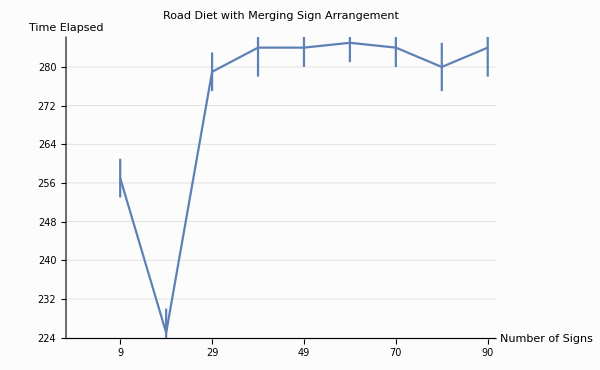

```mathematica
meansampledata=Floor[Mean[samplelist]];
stderrorsampledata=Floor[standardError/@samplelist];
plotData2=Partition[Riffle[meansampledata,stderrorsampledata],2];
tickSpecs2={ {{1,"9"},{2,"19"},{3,"29"},{4,"39"},{5,"49"},{6,"61"},{7,"70"},{8,"82"},{9,"90"},{10,"99"}} ,Automatic};

ErrorListPlot[plotData2, Frame->{Left,Bottom}, Ticks->tickSpecs2,AxesLabel->{Style["Number of Signs",12,FontFamily->"Arial"],Style["Time Elapsed",12,FontFamily->"Arial"]},Joined->True,GridLines->Automatic,PlotLabel->"Road Diet with Merging Sign Arrangement",ImageSize->600,Background->GrayLevel[0.99]]
```

## Animation

```mathematica
somedata=realrundemo[10,{90,180,270,360,450,540,630,720,810,900},1];
```

```mathematica
matrix={};
For[i=1,i≤ 1000,i++,AppendTo[matrix,{0,0}]]
L1=Length[Sampledata[[1]]];
L2=Length[Sampledata[[2]]];
For[i=1,i≤ L1,i++,
p=Sampledata[[1,i,1]];
If[p≤ 1000&&p≠0,matrix[[p,1]]=Red]]
For[i=1,i≤ L2,i++,
p=Sampledata[[2,i,1]];
If[p≤ 1000&&p≠0,matrix[[p,2]]=Blue]] 
{firstlane,secondlane}=Transpose[matrix];
fakefatmatrix={firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane};
ArrayPlot[fakefatmatrix]
```

Part::partd: Part specification Sampledata⟦1⟧ is longer than depth of object.

Part::partd: Part specification Sampledata⟦2⟧ is longer than depth of object.

Part::partd: Part specification Sampledata⟦1,1,1⟧ is longer than depth of object.

Part::partd: Part specification Sampledata⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification Sampledata⟦2,1,1⟧ is longer than depth of object.

Part::partd: Part specification Sampledata⟦2,2,1⟧ is longer than depth of object.

-Graphics-

```mathematica
oneframe[data_,t_]:=Module[
{matrix={},Sampledata,L1,L2},

Sampledata=data[[t]];
L1=Length[Sampledata[[1]]];
L2=Length[Sampledata[[2]]];

For[i=1,i≤ 1000,i++,AppendTo[matrix,{0,0}]];
For[i=1,i≤ L1,i++,
p=Sampledata[[1,i,1]];
If[p≤ 1000&&p≠0,matrix[[p,1]]=Red]];
For[i=1,i≤ L2,i++,
p=Sampledata[[2,i,1]];
If[p≤ 1000&&p≠0,matrix[[p,2]]=Blue]] ;
{firstlane,secondlane}=Transpose[matrix];
fakefatmatrix={firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,firstlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane,secondlane};

ArrayPlot[fakefatmatrix,ImageSize->1000]
]
```

```mathematica
Manipulate[oneframe[somedata,t],{t,1,Length[somedata],1}]
```

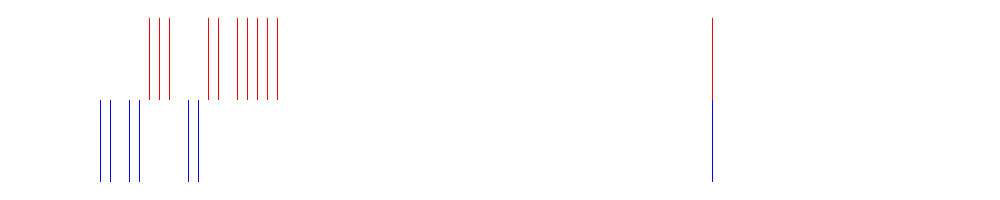

```mathematica
oneframe[somedata,20]
```

```mathematica
Length[somedata]
```

279

```mathematica
(*realrun[SL_,nsign_,TI_]:=Module[
{Lane1={0,0},Lane2={0,0},Lane3={0,0},Lane4={0,0},t=1, process={}},
For[t=0,t≤200,t++,
If[Mod[t,5]==0,
i=RandomInteger[];
If[i<0.25,
AppendTo[Lane4,{0,RandomInteger[{SL-3,SL+3}],0}]
];
If[i≥0.25&&i<0.5,
AppendTo[Lane3,{0,RandomInteger[{SL-3,SL+3}],0}]
];
If[i≥0.5 && i<0.75,
AppendTo[Lane4,{0,RandomInteger[{SL-3,SL+3}],0}]
];
If[i>=0.75 && i<1,
AppendTo[Lane4,{0,RandomInteger[{SL-3,SL+3}],0}]
];
];
If[Length[Lane1]>0&&Length[Lane2]>0 && ,
Lane1=updatev1[Lane1,SL];
Lane2=updatev2[Lane2,SL,1000];
Lane1=updatep1[Lane1];
Lane2=updatep2[Lane2,1000];
Lane2=simplewantomerge[0.2,nsign,Lane2,1000];
{Lane1,Lane2}=merge[Lane1,Lane2];
];
AppendTo[process,{Lane1,Lane2}];
];
process
]*)
```

```mathematica
(*updatev[list_,SL_]
 updatep[list_]
 simplewantemerge[p_,listofsign_,list_]
 merge[list1_,list2_]
*)
```